```mathematica
56.^4
```

9.8345×10^6

```mathematica
820*(10^3)/(10^2)^3
```

41/50

1

1.67262×10^-24

1

1

2

1

1

1.60218×10^-6

1.60218×10^-6 Emev

386.803 Emev

0.5

1

30000000

(0.0637606-0.0637606 ⅇ^-x)/x^3

1.73542/x^3

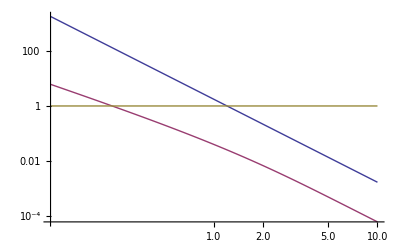

```mathematica
rhob=10^(0)
nb=rhob*mp
gbf=1
n=1
A=2
Z=A/2
gff=1
Ephoton=1*ergPmev
Clear[Ephoton]
Ephoton=Emev*ergPmev
x=Ephoton/(kb*T)
Clear[x]
fe=0.5
fi=1
T=3*10^7
sigmaff=FullSimplify[mp*1.50*10^(25)*(fe*fi*Z^2/A)*rhob*T^(-3.5)*gff*(1-Exp[-x])/x^3/sigmat]
sigmabf=2.82*10^(29)*Z^4/(n^5)*gbf/(kb*T*x/h)^3/sigmat
(*LogLogPlot[{sigmabf,sigmaff,1},{Emev,1/10000,10}]*)
LogLogPlot[{sigmabf,sigmaff,1},{x,.1,10}]
```

```mathematica
sigmabf//.{Ephoton->ergPmev/10000}
sigmabf//.{Ephoton->ergPmev*10}
```

29987.1

2.99871×10^-11

```mathematica
sigmaff//.{Ephoton->ergPmev*10}
sigmaff//.{Ephoton->ergPmev*10}
```

1.10175×10^-13

1.10175×10^-13

```mathematica
kb*T/ergPmev
```

0.0025853

```mathematica
sigmaff
sigmabf
```

1.17545×10^-25

1.24672×10^-24

```mathematica
Z=17.
Clear[Z]
Yz=10^(-2)*10^(-Z/5)
```

17.

10^(-2-Z/5)

```mathematica
Clear[z,n]
Integrate[z^4*Exp[-z],{z,0,Infinity}]
```

24

```mathematica
24*(5/Log[10])^4.
```

533.616

```mathematica
(5/Log[10.])
```

2.17147

```mathematica
2^4
```

16

```mathematica
Clear[z,a,x]
FullSimplify[Integrate[z^4*Exp[-z],{z,0,Infinity}]/Integrate[Exp[-z],{z,0,Infinity}]]
```

24

```mathematica
24*16
```

384